```mathematica
Quiet[Remove["Global`*"]]
Needs["VariationalMethods`"]
```

## Task 1: Shortest distance problem

#### 1.1

```mathematica
F[y_,dy_,x_]:=Sqrt[1+dy^2]
```

```mathematica
phi[y_]:=Integrate[F[y,y'[x],x],{x,a,b}]
```

```mathematica
phi[y]
```

∫_a^b √(1+y'[x]^2)ⅆx

```mathematica
phi[Function[x,x]]/.{a->1,b->2}
```

√2

#### 1.2

```mathematica
GeneralSol=EulerEquations[F[y[x],y'[x],x],y[x],x]
```

-y''[x]/((1+y'[x]^2)^(3/2))==0

```mathematica
ysol=DSolve[GeneralSol,y[x],x][[1,1,2]]
```

C[1]+x C[2]

#### 1.3

```mathematica
GeneralSol/.{y'[x] -> D[ysol,x],y''[x] -> D[ysol,{x,2}]}
```

True

#### 1.4

```mathematica
ysol=DSolve[{GeneralSol,y[10]==5,y[15]==7},y[x],x][[1,1,2]]//Simplify
```

1+(2 x)/5

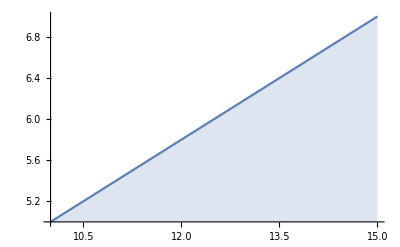

```mathematica
Plot[ysol,{x,10,15},Filling->Bottom]
```

## Task 2 Catenary problem

#### Define given functions

```mathematica
Clear[F,phi,ysol,ySol,GeneralSol]
```

```mathematica
F[y_,yd_,x_]:=y Sqrt[1+yd^2]
```

```mathematica
G[y_,yd_,x_]:=Sqrt[1+yd^2]
```

```mathematica
phia[y_,yd_,x_]:=F[y,yd,x] + La G[y,yd,x]
```

```mathematica
L[y_]:=Integrate[G[y,D[y,x],x],{x,-5,5}]
```

```mathematica
La[y_]:=NIntegrate[G[y,D[y,x],x],{x,-5,5}]
```

```mathematica
sol=EulerEquations[phia[y[x],y'[x],x],y[x],x]
(* Neccessary condition for the functional to become stationary *)
```

(1+y'[x]^2-(La+y[x]) y''[x])/((1+y'[x]^2)^(3/2))==0

### Solving with first integrals

```mathematica
f1=FirstIntegrals[phia[y[x],y'[x],x],y[x],x][[1,2]]
```

(-La-y[x])/(√(1+y'[x]^2))

```mathematica
yd=Solve[f1==C1,y'[x]][[1,1,2]]
```

Solve::nongen: Solutions may not be valid for all values of parameters.

-(√(-C1^2+La^2+2 La y[x]+y[x]^2))/C1

#### Solving with separation variables

```mathematica
xd=Integrate[1/yd,y[x]]+C2
```

C2-C1 Log[La+y[x]+√(-C1^2+La^2+2 La y[x]+y[x]^2)]

```mathematica
ysol=Solve[x==xd,y[x]][[1,1,2]]
```

Solve::nongen: Solutions may not be valid for all values of parameters.

1/2 (ⅇ^(C2/C1-x/C1)+C1^2 ⅇ^(-C2/C1+x/C1)-2 La)

#### Show result satisfies neccessary condition

```mathematica
sol1=(ysol/.x->-5)==10;
```

```mathematica
sol2=(ysol/.x->5)==10;
```

```mathematica
sol3=(L[ysol])==20;
```

```mathematica
solu=FindRoot[{sol1,sol2,sol3},{{C1,1},{C2,1},{La,1}}]
```

{C1→2.2964,C2→1.9091,La→0.260286}

```mathematica
ysol=ysol/.solu
```

1/2 (-0.520571+ⅇ^(0.831344-0.435464 x)+5.27346 ⅇ^(-0.831344+0.435464 x))

```mathematica
(* Check the length *) 
La[ysol]
```

20.

```mathematica
(* Check variational derivative has vanished *)
```

```mathematica
sol/.{y[x]->ysol,y'[x]->D[ysol,x],y''[x] -> D[ysol,{x,2}],La->0.2602857093791088}//Simplify
```

True

#### Plot

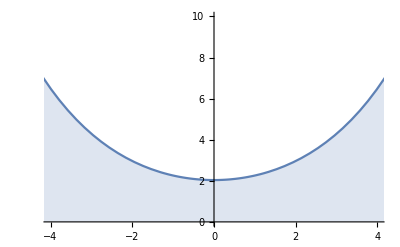

```mathematica
Plot[ysol,{x,-5,5},PlotRange->{{-4,4},{0,10}},Filling->Axis]
```